## Elastic map contour plots for examples in Tape and Tape (2022).

#### First run the notebook ES_ContourPlots.nb. Then set the view direction for the balls:

```mathematica
(* eye=10xyzTP[{90Degree,0Degree}]; *)
eye={-0.1,0,10};
```

#### Then execute this composite command:

```mathematica
ContourPlotsForTmat[Tmat_]:=(cpFprelim=ContourPlot[fOnSphere[Tmat,{θ,ϕ}],{θ,0,2π},{ϕ,0,π}];
cpF=Graphics3D[GraphicsComplex[xyzTP/@cpFprelim[[1,1]],cpFprelim[[1,2]]]];
GraphicsRow[{
Show[cpFprelim,AspectRatio->Automatic,FrameTicks->{Range[0,2π,π/2],Range[0,π,π/2]},ImageSize->550],
Show[cpF,Boxed->False,Lighting->"Neutral",ViewPoint->eye]},Spacings->-100])
```

## TRIVIAL for Ref matrix for the collage. Round entries to, say, six places if you want.

```mathematica
TmatTRIVrefMat=({{4.086056425972008, 0.010701286581823899, -0.476223441320207, 0.9170182608458065, -0.8185646932351285, -0.3402483127712459}, {0.010701286581823899, 4.672938167924996, -0.37683440698972154, 0.29352287634134655, -0.962574548964882, -1.6122730335263864}, {-0.476223441320207, -0.37683440698972154, 2.5108800080246434, 0.026713327098956616, 0.5120960985918724, -0.6943672528612547}, {0.9170182608458065, 0.2935228763413468, 0.026713327098956616, 4.216229915649152, 0.3843316097198629, 0.17306101258392592}, {-0.8185646932351285, -0.962574548964882, 0.5120960985918724, 0.3843316097198629, 2.9861331131213396, 0.09753435587151948}, {-0.340248312771246, -1.6122730335263862, -0.694367252861255, 0.17306101258392592, 0.09753435587151948, 2.527762369307859}});
```

```mathematica
ContourPlotsForTmat[TmatTRIVrefMat]
```

## MONO for Ref matrix for the collage

```mathematica
TmatMONOrefMat=({{1.25, -0.4330127018922193, 0, 0, 0, 0}, {-0.4330127018922193, 1.7500000000000002, 0, 0, 0, 0}, {0, 0, 4.635052873539182, -0.06468644906460641, -0.7502933778165867, -0.15527238292187495}, {0, 0, -0.06468644906460641, 4.265283351323687, 0.7760261745747741, 1.0818796331939078}, {0, 0, -0.7502933778165867, 0.7760261745747739, 4.2435833842806385, 0.056114869469269024}, {0, 0, -0.15527238292187495, 1.0818796331939078, 0.056114869469269024, 4.856080390856493}});
```

```mathematica
ContourPlotsForTmat[TmatMONOrefMat]
```

## ORTH for Ref matrix for the collage

```mathematica
TmatORTHrefMat=({{1, 0, 0, 0, 0, 0}, {0, 3, 0, 0, 0, 0}, {0, 0, 5, 0, 0, 0}, {0, 0, 0, 2.4272563250434462, -0.3233822395019309, 0.2077424464564211}, {0, 0, 0, -0.32338223950193085, 1.6147225215909469, -0.14089085588492373}, {0, 0, 0, 0.20774244645642115, -0.14089085588492373, 3.9580211533656118}});
```

```mathematica
ContourPlotsForTmat[TmatORTHrefMat]
```

## TRIG for Ref matrix for the collage :

```mathematica
TmatTRIGrefMat=({{1.5, 0, -0.8660254, 0, 0, 0}, {0, 1.5, 0, -0.8660254, 0, 0}, {-0.8660254, 0, 2.5, 0, 0, 0}, {0, -0.8660254, 0, 2.5, 0, 0}, {0, 0, 0, 0, 5.5, -0.5}, {0, 0, 0, 0, -0.5, 5.5}});
```

```mathematica
ContourPlotsForTmat[TmatTRIGrefMat]
```

## TET for Ref matrix for the collage :

```mathematica
TmatTETrefMat=({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 3, 0, 0, 0}, {0, 0, 0, 6, 0, 0}, {0, 0, 0, 0, 5, -1}, {0, 0, 0, 0, -1, 5}});
```

```mathematica
ContourPlotsForTmat[TmatTETrefMat]
```

## CUBE for Ref matrix for the collage :

```mathematica
TmatCUBErefMat=({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 2, 0, 0}, {0, 0, 0, 0, 2, 0}, {0, 0, 0, 0, 0, 3}});
```

```mathematica
ContourPlotsForTmat[TmatCUBErefMat]
```

## XISO for Ref matrix for the collage

```mathematica
TmatXISOrefMat=({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 2, 0, 0, 0}, {0, 0, 0, 2, 0, 0}, {0, 0, 0, 0, 3, 2.5}, {0, 0, 0, 0, 2.5, 4}});
```

```mathematica
ContourPlotsForTmat[TmatXISOrefMat]
```

## The ALT examples are for Figure 5

## ALT MONO

```mathematica
TmatALTMONOrefMat=({{0.655911704820046, 0.34018452880250205, 0, 0, 0, 0}, {0.34018452880250205, -0.6708257289750934, 0, 0, 0, 0}, {0, 0, 0.1408968195741056, 0.4512270978737538, 0.40089407062961646, -0.796818087284771}, {0, 0, 0.4512270978737538, 0.4095569162206085, 0.07149811281325569, -0.8888434230632241}, {0, 0, 0.40089407062961646, 0.07149811281325569, 0.3353105456395493, 0.694828769728074}, {0, 0, -0.796818087284771, -0.8888434230632241, 0.694828769728074, -0.05693100258157546}});
```

```mathematica
ContourPlotsForTmat[TmatALTMONOrefMat]
```

## ALT TRIG

```mathematica
(* TmatALTTRIGrefMat=TmatForTRIG/.{a->1,c->3.5,e->3,f->4.5,k->5,m->2.5}; *)
```

```mathematica
TmatALTTRIGrefMat=({{1, 0, 2.5, 0, 0, 0}, {0, 1, 0, 2.5, 0, 0}, {2.5, 0, 3.5, 0, 0, 0}, {0, 2.5, 0, 3.5, 0, 0}, {0, 0, 0, 0, 3, 5}, {0, 0, 0, 0, 5, 4.5}});
```

```mathematica
ContourPlotsForTmat[TmatALTTRIGrefMat]
```

## ALT TET

```mathematica
(* TmatALTTETrefMat=TmatForTET/.{a->4,c->2.5,d->7,e->5,f->6,k->2.5}; *)
```

```mathematica
TmatALTTETrefMat=({{4, 0, 0, 0, 0, 0}, {0, 4, 0, 0, 0, 0}, {0, 0, 2.5, 0, 0, 0}, {0, 0, 0, 7, 0, 0}, {0, 0, 0, 0, 5, 2.5}, {0, 0, 0, 0, 2.5, 6}});
```

```mathematica
ContourPlotsForTmat[TmatALTTETrefMat]
```

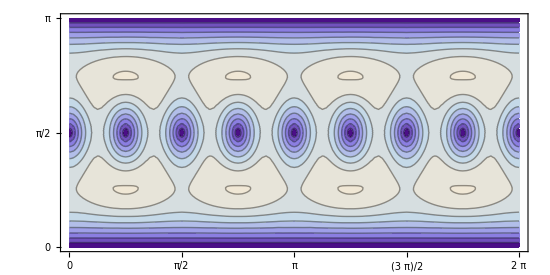

## ALT XISO

```mathematica
(* TmatALTXISOrefMat=TmatForXISO/.{a->1,c->2,e->3,f->4,k->0}; *)
```

```mathematica
TmatALTXISOrefMat=({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 2, 0, 0, 0}, {0, 0, 0, 2, 0, 0}, {0, 0, 0, 0, 3, 0}, {0, 0, 0, 0, 0, 4}});
```

```mathematica
ContourPlotsForTmat[TmatALTXISOrefMat]
```

## ISO (the solid blue ball) (this trivial plot requires running common_funs and common_MTfuns)

```mathematica
(* eye={82.13938048432696,38.3022221559489,42.261826174069945};
eye=100xyztp[{25,65}];
PrintEye; *)
```

```mathematica
(* TwoFoldISO=Graphics3D[{
{Hue[.58,.8,.5],EdgeForm[],Polygon/@Select[SpherePolyList[1,0,360,0,180,5.,5.],SeeOnSphere[#[[1]],1,eye]&]},      
},ViewPoint->eye,Lighting->"Neutral",Boxed->False] *)
```